```mathematica
data=ToExpression[Import["F:\\0.2\\巡线\\data\\TCRT 1~3.txt","Text"]];
```

```mathematica
l=#[[1]]&/@data;
m=#[[2]]&/@data;
r=#[[3]]&/@data;
```

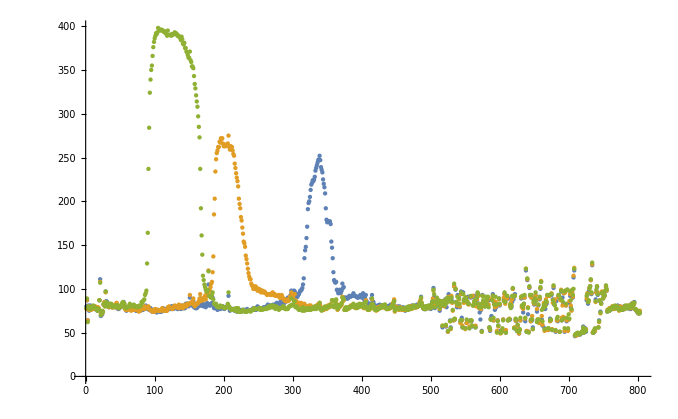

```mathematica
ListPlot[{l,m,r},PlotRange->All]
```

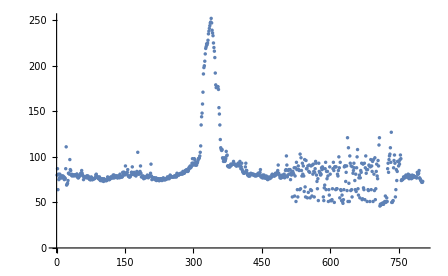
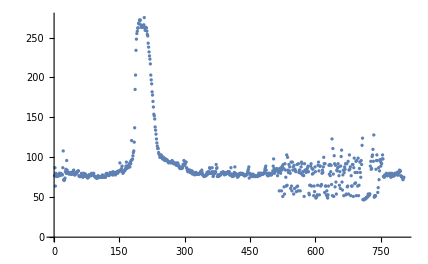
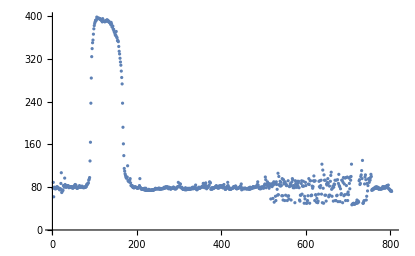

```mathematica
{ListPlot[l,PlotRange->All],ListPlot[m,PlotRange->All],ListPlot[r,PlotRange->All]}
```

```mathematica
x1=310;
y1=350;
Grid[{#[[1]]&/@data[[x1;;y1]],#[[2]]&/@data[[x1;;y1]],#[[3]]&/@data[[x1;;y1]]},Frame->All]
x2=180;
y2=220;
Grid[{#[[1]]&/@data[[x2;;y2]],#[[2]]&/@data[[x2;;y2]],#[[3]]&/@data[[x2;;y2]]},Frame->All]
x3=80;
y3=180;
Grid[{#[[1]]&/@data[[x3;;y3]],#[[2]]&/@data[[x3;;y3]],#[[3]]&/@data[[x3;;y3]]},Frame->All]
```

96 | 98 | 98 | 99 | 101 | 105 | 112 | 135 | 144 | 148 | 158 | 171 | 191 | 198 | 200 | 205 | 213 | 219 | 221 | 224 | 223 | 225 | 228 | 235 | 238 | 241 | 244 | 247 | 248 | 252 | 247 | 239 | 236 | 233 | 225 | 220 | 216 | 209 | 192 | 179 | 176
82 | 82 | 84 | 81 | 83 | 81 | 80 | 83 | 79 | 80 | 80 | 80 | 79 | 78 | 81 | 79 | 81 | 79 | 79 | 79 | 79 | 79 | 79 | 80 | 79 | 80 | 82 | 80 | 81 | 84 | 81 | 78 | 78 | 77 | 76 | 76 | 77 | 77 | 78 | 77 | 78
76 | 76 | 76 | 77 | 75 | 79 | 76 | 75 | 76 | 76 | 76 | 78 | 76 | 76 | 76 | 78 | 76 | 77 | 77 | 77 | 79 | 77 | 80 | 78 | 77 | 80 | 78 | 78 | 80 | 84 | 78 | 76 | 75 | 76 | 77 | 78 | 79 | 80 | 78 | 78 | 79

82 | 81 | 83 | 84 | 90 | 82 | 78 | 78 | 79 | 78 | 79 | 76 | 77 | 78 | 77 | 77 | 78 | 78 | 78 | 80 | 78 | 77 | 78 | 79 | 79 | 79 | 82 | 92 | 79 | 75 | 77 | 76 | 76 | 77 | 77 | 76 | 75 | 75 | 77 | 74 | 75
98 | 102 | 106 | 108 | 119 | 137 | 185 | 203 | 234 | 248 | 255 | 258 | 262 | 262 | 268 | 267 | 272 | 271 | 272 | 266 | 263 | 263 | 263 | 263 | 265 | 264 | 266 | 275 | 262 | 259 | 263 | 262 | 262 | 258 | 254 | 252 | 243 | 238 | 232 | 227 | 223
92 | 90 | 92 | 93 | 96 | 88 | 83 | 83 | 82 | 83 | 80 | 80 | 79 | 79 | 79 | 81 | 80 | 80 | 80 | 79 | 79 | 78 | 78 | 79 | 79 | 80 | 83 | 96 | 80 | 78 | 77 | 76 | 77 | 76 | 77 | 77 | 76 | 75 | 78 | 77 | 74

76 | 76 | 76 | 76 | 77 | 77 | 80 | 81 | 78 | 78 | 77 | 78 | 76 | 76 | 78 | 75 | 74 | 76 | 74 | 74 | 76 | 74 | 74 | 73 | 76 | 75 | 75 | 74 | 74 | 74 | 74 | 75 | 78 | 77 | 76 | 75 | 75 | 77 | 76 | 78 | 77 | 78 | 77 | 77 | 80 | 77 | 80 | 77 | 78 | 79 | 78 | 79 | 79 | 77 | 77 | 79 | 78 | 79 | 77 | 81 | 79 | 78 | 78 | 78 | 78 | 83 | 81 | 83 | 83 | 80 | 81 | 90 | 82 | 82 | 81 | 83 | 86 | 79 | 79 | 78 | 78 | 78 | 79 | 80 | 83 | 83 | 89 | 81 | 81 | 81 | 83 | 80 | 81 | 81 | 79 | 81 | 84 | 83 | 105 | 81 | 82
78 | 77 | 78 | 78 | 77 | 77 | 80 | 78 | 79 | 79 | 78 | 80 | 77 | 76 | 76 | 75 | 75 | 74 | 74 | 76 | 74 | 77 | 75 | 76 | 75 | 76 | 75 | 75 | 75 | 76 | 75 | 78 | 76 | 76 | 75 | 76 | 75 | 75 | 75 | 79 | 79 | 80 | 78 | 78 | 78 | 78 | 77 | 78 | 80 | 81 | 80 | 80 | 79 | 80 | 78 | 82 | 78 | 80 | 79 | 81 | 80 | 78 | 80 | 80 | 82 | 81 | 80 | 82 | 83 | 82 | 83 | 93 | 84 | 84 | 83 | 86 | 89 | 82 | 80 | 81 | 83 | 83 | 83 | 84 | 86 | 89 | 94 | 86 | 89 | 89 | 87 | 88 | 90 | 92 | 88 | 94 | 92 | 96 | 121 | 97 | 98
81 | 85 | 84 | 86 | 87 | 88 | 93 | 95 | 98 | 129 | 164 | 237 | 284 | 324 | 339 | 350 | 355 | 366 | 376 | 382 | 386 | 389 | 392 | 391 | 393 | 398 | 395 | 396 | 396 | 395 | 396 | 395 | 395 | 394 | 393 | 394 | 392 | 391 | 389 | 395 | 390 | 390 | 390 | 390 | 389 | 391 | 390 | 391 | 391 | 393 | 391 | 392 | 391 | 389 | 389 | 389 | 387 | 387 | 384 | 388 | 385 | 380 | 379 | 381 | 375 | 375 | 371 | 370 | 367 | 364 | 364 | 371 | 361 | 359 | 354 | 354 | 352 | 343 | 334 | 329 | 321 | 314 | 308 | 297 | 285 | 273 | 237 | 192 | 161 | 139 | 115 | 110 | 105 | 102 | 99 | 97 | 97 | 99 | 120 | 92 | 92

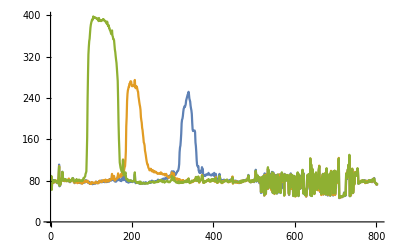

```mathematica
ListLinePlot[{l,m,r},PlotRange->All]
```

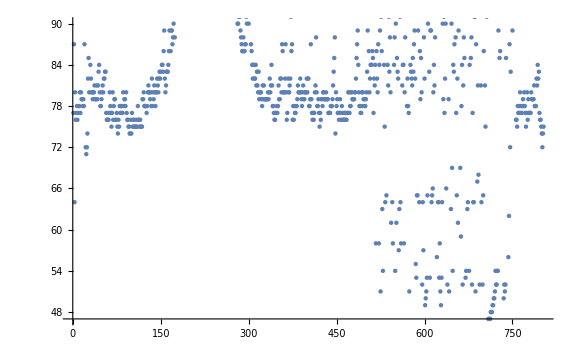

```mathematica
ListPlot[m,PlotRange->{47,90},ImageSize->Large]
```

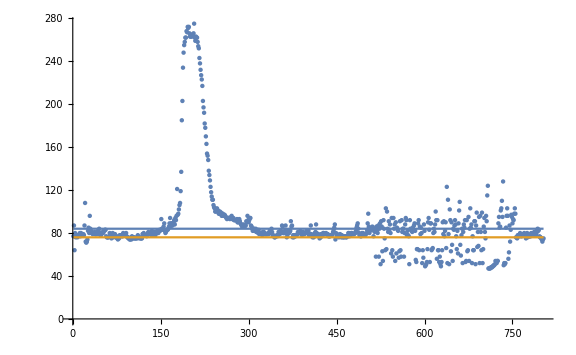

```mathematica
Show[ListPlot[m,PlotRange->All,ImageSize->Large],Plot[{y=84,y=76},{x,1,803},ImageSize->Large]]
```

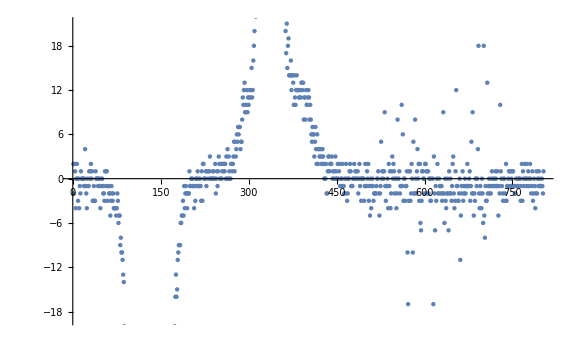

```mathematica
ListPlot[l-r,ImageSize->Large]
```

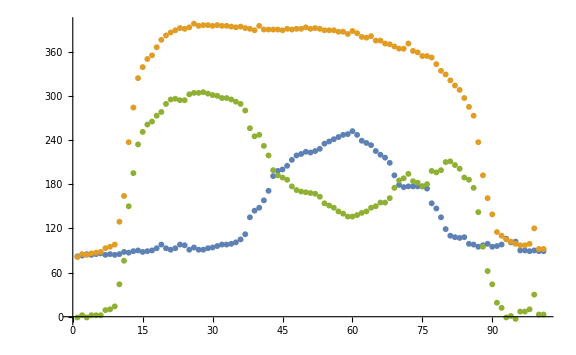

```mathematica
ListPlot[{l[[280;;380]],r[[80;;180]],-l[[280;;380]]+r[[80;;180]]},PlotRange->All,ImageSize->Large]
```

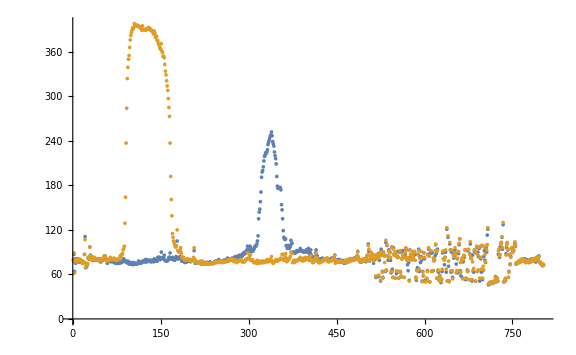
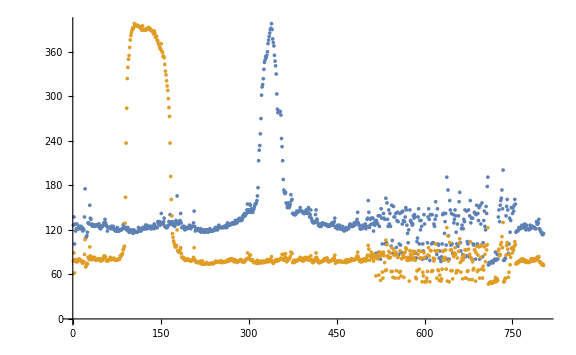
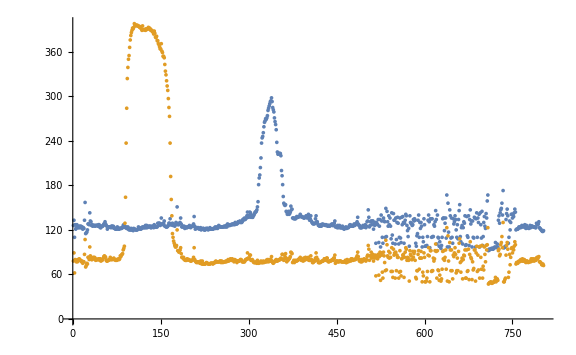
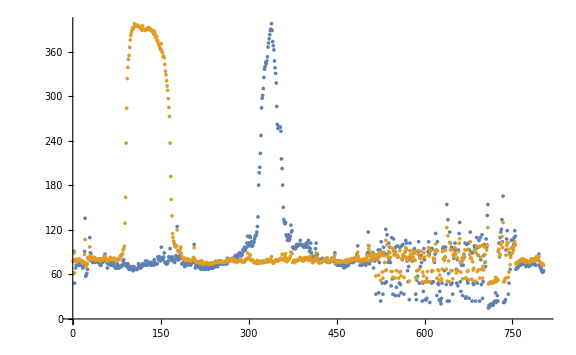

```mathematica
{ListPlot[{l,r},PlotRange->All,ImageSize->Large],ListPlot[{l*398/252,r},PlotRange->All,ImageSize->Large],ListPlot[{l+298-252,r},PlotRange->All,ImageSize->Large],ListPlot[{(l-80)*(398-78)/(252-80)+78,r},PlotRange->All,ImageSize->Large]}
```

```mathematica
x1=200;
y1=250;
Grid[{#[[1]]&/@data[[x1;;y1]],#[[2]]&/@data[[x1;;y1]],#[[3]]&/@data[[x1;;y1]]},Frame->All]
x1=50;
y1=100;
Grid[{#[[1]]&/@data[[x1;;y1]],#[[2]]&/@data[[x1;;y1]],#[[3]]&/@data[[x1;;y1]]},Frame->All]
```

78 | 77 | 78 | 79 | 79 | 79 | 82 | 92 | 79 | 75 | 77 | 76 | 76 | 77 | 77 | 76 | 75 | 75 | 77 | 74 | 75 | 75 | 76 | 76 | 74 | 74 | 74 | 76 | 75 | 76 | 76 | 74 | 75 | 75 | 77 | 75 | 75 | 75 | 75 | 75 | 76 | 76 | 76 | 78 | 76 | 77 | 78 | 76 | 78 | 80 | 79
263 | 263 | 263 | 263 | 265 | 264 | 266 | 275 | 262 | 259 | 263 | 262 | 262 | 258 | 254 | 252 | 243 | 238 | 232 | 227 | 223 | 217 | 203 | 197 | 192 | 182 | 178 | 170 | 163 | 154 | 152 | 148 | 138 | 134 | 129 | 123 | 118 | 114 | 111 | 111 | 106 | 104 | 103 | 100 | 100 | 101 | 103 | 100 | 101 | 98 | 98
79 | 78 | 78 | 79 | 79 | 80 | 83 | 96 | 80 | 78 | 77 | 76 | 77 | 76 | 77 | 77 | 76 | 75 | 78 | 77 | 74 | 78 | 74 | 74 | 74 | 74 | 74 | 75 | 76 | 75 | 75 | 74 | 74 | 74 | 74 | 75 | 75 | 75 | 75 | 74 | 75 | 76 | 76 | 76 | 78 | 77 | 77 | 77 | 77 | 77 | 77

79 | 79 | 80 | 82 | 82 | 85 | 82 | 80 | 79 | 75 | 78 | 78 | 78 | 78 | 78 | 77 | 79 | 79 | 77 | 79 | 78 | 76 | 76 | 75 | 75 | 75 | 78 | 77 | 75 | 75 | 76 | 76 | 76 | 76 | 77 | 77 | 80 | 81 | 78 | 78 | 77 | 78 | 76 | 76 | 78 | 75 | 74 | 76 | 74 | 74 | 76
80 | 81 | 80 | 82 | 82 | 83 | 83 | 77 | 76 | 76 | 76 | 76 | 77 | 80 | 78 | 77 | 75 | 77 | 80 | 76 | 78 | 79 | 79 | 76 | 76 | 77 | 75 | 74 | 76 | 75 | 78 | 77 | 78 | 78 | 77 | 77 | 80 | 78 | 79 | 79 | 78 | 80 | 77 | 76 | 76 | 75 | 75 | 74 | 74 | 76 | 74
79 | 80 | 82 | 84 | 85 | 84 | 83 | 79 | 78 | 78 | 79 | 79 | 80 | 80 | 83 | 80 | 80 | 81 | 80 | 81 | 82 | 80 | 80 | 79 | 80 | 79 | 80 | 80 | 81 | 80 | 81 | 85 | 84 | 86 | 87 | 88 | 93 | 95 | 98 | 129 | 164 | 237 | 284 | 324 | 339 | 350 | 355 | 366 | 376 | 382 | 386

```mathematica
(lv-80)*(398-78)/(252-80)+78-rv//Simplify
```

78+80/43 (-80+lv)-rv

```mathematica
N@%
```

78.+1.86047 (-80.+lv)-1. rv

```mathematica
N[80/43,10]
```

1.860465116

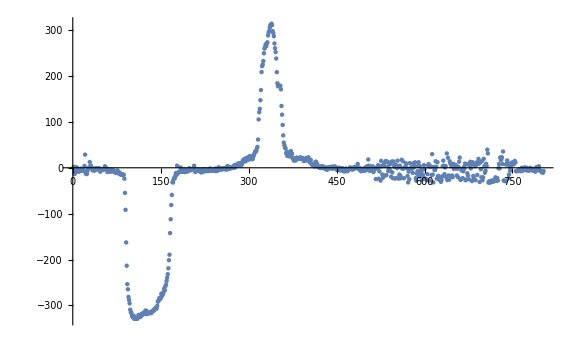

```mathematica
ListPlot[{(l-80)*(398-78)/(252-80)+78-r},PlotRange->All,ImageSize->Large]
```

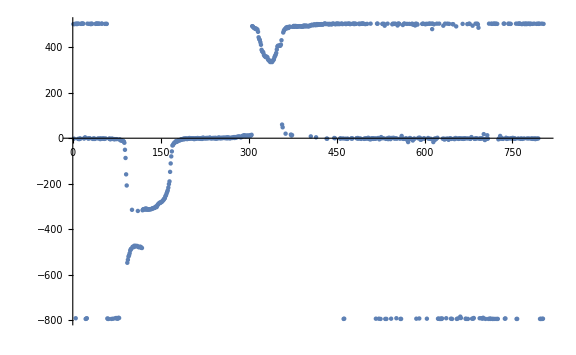

```mathematica
Lm=252;
Lt=84;
Rm=398;
Rt=76;
temp=If[#[[2]]≤ Lt&&#[[1]]≥#[[3]],2Lm-(#[[1]]-#[[3]]),If[#[[2]]≤ Rt&&#[[1]]<#[[3]],-2Rm-(#[[1]]-#[[3]]),#[[1]]-#[[3]]]]&/@data;
ListPlot[temp,ImageSize->Large]
```